```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/manuscript/graphs

```mathematica
hbarc=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbarc)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Select[Import["/home/kirscher/Documents/vault/Vorlesungen/num_methods/lec_ex0_b2.22.dat","Table"][[2;;]],#[[3]]!=-1.&];
activeLEC=activeLEC[[;;;;6]]
```

{{8.,-974.194,-1105.1,0.},{14.,-1668.47,-1537.32,0.},{20.,-2357.36,-1788.28,4.46},{26.,-3043.2,-1896.75,4.88},{32.,-3727.18,-1971.84,0.},{38.,-4409.67,-1973.3,5.62}}

```mathematica
(*one dimer to rule them all*)
eCore=2.2;
dimerCore={{0.1238935700962293,1.6864377554283103},{0.26233165527224883,0.2110287548871554},{0.5702975963884093,0.024061462515210734}};
```

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (1/2^(9/2)) (Pi/((core[[i]][[2]]+core[[j]][[2]]) (core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];

VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta1,eta2,eta3,w1,w2,w3},
eta1=(π^(3/2) Cc)/(2 (lam Bb+Gg(lam+2Bb)+lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh))^(3/2));
w1=(2lam(Aa+Bb)(Gg+Hh))/(lam Bb+Gg(lam+2Bb)+lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh));
eta2=(π/(2 (lam+Aa+Bb)(lam+Gg+Hh)))^(3/2)Dd/4;
w2=(2lam(Aa+Bb))/(lam+Aa+Bb);
eta3=(π^(3/2) Dd)/(4 (2 lam^2+lam Bb+Gg(5lam+2Bb)+5lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh))^(3/2));
w3=(2lam (2lam+Aa+Bb)(Gg+Hh))/(2 lam^2+lam Bb+Gg(5lam+2Bb)+5lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh));
eta1 Exp[-w1 r^2]+eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

AppendTo[Wmats,cij amat];
(*AppendTo[Wmats,cij amat];*)

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];
relerr=Norm[Amat.usol-bcol]/Norm[usol];
(*Print["relative error in wave-function solution = ",relerr];*)

(*tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);*)
sol=NSolve[usol⟦-1⟧==RiccatiBesselJ[momentum Rdis,Lin]-RiccatiBesselN[momentum Rdis,Lin] xx,xx,Reals];
tanDelta=xx/.sol[[-1]];
t2=AbsoluteTime[];
(*Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins     p_match·r_max = ",momentum Rdis];*)
{tanDelta,usol}
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,LECd_,energ_:0.001]:=Module[{locall=l},
momFM=Sqrt[mh2 energ];
{TanDelSwave,wfkt}=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
{-TanDelSwave/Sqrt[mh2 energ ],wfkt}
]
```

alternative to the stochastic and inefficient search for an appropriate basis, one can invoke a genetic optimization (external Python/Fortran program, look for <bridgeA2_tmp.py> and calls therein)
and feed the results to the function <CalcDimerE[]> (see above

Using λ=14.fm^-2     C=-1668.47MeV     D=-1537.32MeV    2-body scale B(2)=2.22MeV    3-body scale B(3)=8.48MeV

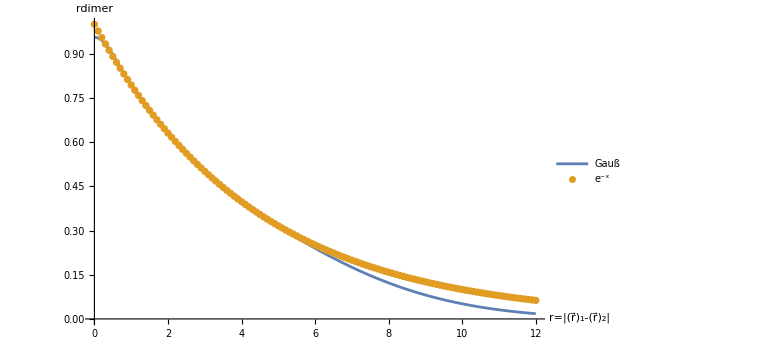

```mathematica
lambdas=activeLEC[[All,1]];
lambdaTest=lambdas[[2]];

LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[3]];
Print["Using λ=",Style[lambdaTest,Red],"fm^-2     C=",Style[LECc,Red],"MeV     D=",Style[LECd,Red],"MeV    2-body scale B(2)=",Style[2.22,Red],"MeV    3-body scale B(3)=",Style[8.48,Red],"MeV"];

JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@dimerCore];rR=Range[0,12,0.100];
JacobiTrailWavefunctionDataU=Table[JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];

plotData=Transpose[{rR,JacobiTrailWavefunctionDataU}];
plotDataExp=Table[{rr,Exp[-(√(Mm eCore))/hbarc rr]},{rr,rR}];
lgd={"Gauß","e^-x"};

ListPlot[{Transpose[{rR,plotData[[All,2]]}],Transpose[{rR,plotDataExp[[All,2]]}]},AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large,PlotLabels->Automatic,Joined->{True,False}]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.1;
(* Integration grid *)
rMa=8;
grdPerFermi=5;
nGrd=IntegerPart[rMa grdPerFermi];
results={};

Do[

LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lam&]][[3]];

tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,LECd,energ][[1]];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,eCore,tmp,tmp/(hbarc/√(Mm Abs[eCore]))}];
Print["λ=",lam,"  C_0(λ)=",LECc,"  D_0(λ)=",LECd,")  ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbarc/√(Mm Abs[eCore]))];
,{lam,lambdas}];
```

λ=8.  C_0(λ)=-974.194  D_0(λ)=-1105.1)  ; R_max=8 ; #=40 ; E_match=0.1 ; a_dd=-1.92076 ; a_dd/a_aa=-0.442383

λ=14.  C_0(λ)=-1668.47  D_0(λ)=-1537.32)  ; R_max=8 ; #=40 ; E_match=0.1 ; a_dd=-4.50486 ; a_dd/a_aa=-1.03754

λ=20.  C_0(λ)=-2357.36  D_0(λ)=-1788.28)  ; R_max=8 ; #=40 ; E_match=0.1 ; a_dd=-10.1806 ; a_dd/a_aa=-2.34476

λ=26.  C_0(λ)=-3043.2  D_0(λ)=-1896.75)  ; R_max=8 ; #=40 ; E_match=0.1 ; a_dd=-33.8332 ; a_dd/a_aa=-7.79234

λ=32.  C_0(λ)=-3727.18  D_0(λ)=-1971.84)  ; R_max=8 ; #=40 ; E_match=0.1 ; a_dd=67.6104 ; a_dd/a_aa=15.5718

λ=38.  C_0(λ)=-4409.67  D_0(λ)=-1973.3)  ; R_max=8 ; #=40 ; E_match=0.1 ; a_dd=21.5879 ; a_dd/a_aa=4.97204

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

λ = 8.   C_0(λ) = -974.194   D_0(λ) = -1105.1     R_max = 37     #(grid points) = 444                a_dd = -9.85839 fm        a_dd/a_aa = -2.27055

λ = 14.   C_0(λ) = -1668.47   D_0(λ) = -1537.32     R_max = 37     #(grid points) = 444                a_dd = -4.91428 fm        a_dd/a_aa = -1.13184

λ = 20.   C_0(λ) = -2357.36   D_0(λ) = -1788.28     R_max = 37     #(grid points) = 444                a_dd = -3.51355 fm        a_dd/a_aa = -0.809228

λ = 26.   C_0(λ) = -3043.2   D_0(λ) = -1896.75     R_max = 37     #(grid points) = 444                a_dd = -2.82441 fm        a_dd/a_aa = -0.650507

λ = 32.   C_0(λ) = -3727.18   D_0(λ) = -1971.84     R_max = 37     #(grid points) = 444                a_dd = -2.40536 fm        a_dd/a_aa = -0.553993

λ = 38.   C_0(λ) = -4409.67   D_0(λ) = -1973.3     R_max = 37     #(grid points) = 444                a_dd = -2.11947 fm        a_dd/a_aa = -0.488148

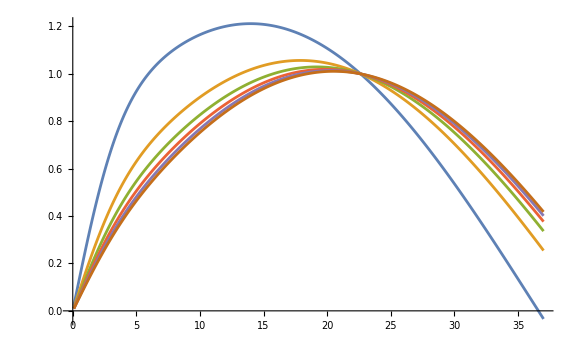

```mathematica
grdPerFermi=12;
rMax=37;
nGrd=IntegerPart[rMax grdPerFermi];
Grd=Range[0,rMax,1/grdPerFermi][[2;;]];

results={};
resultsWF={};
runtimes={};

(*SetSharedVariable[results,resultsPhases];*)
Do[

LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lam&]][[3]];
ta=AbsoluteTime[];
{tmp,tmp2}=GetEREP3[lam,rMax,nGrd,dimerCore,LECc,LECd,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[resultsWF,Transpose[{Grd,tmp2}]];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["λ = ",lam,"   C_0(λ) = ",LECc,"   D_0(λ) = ",LECd,"     R_max = ",rMax,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbarc/√(Mm Abs[eCore])),Red,18]];
,{lam,lambdas}]

ListPlot[resultsWF,Joined->True,PlotRange->Full,ImageSize->Large]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -9.98127     a_dd/a_aa = -2.29885

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -5.0075     a_dd/a_aa = -1.15331

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -3.60197     a_dd/a_aa = -0.829593

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -2.91105     a_dd/a_aa = -0.670461

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -2.4911     a_dd/a_aa = -0.573741

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -2.20468     a_dd/a_aa = -0.507774

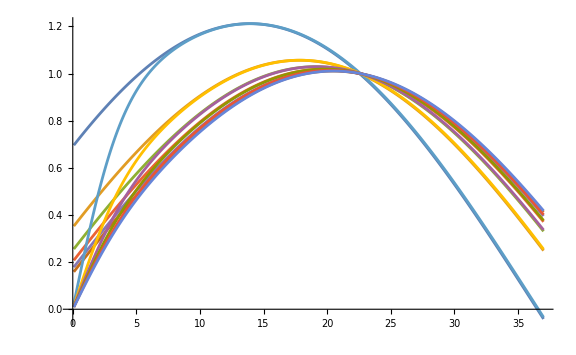

```mathematica
momFM=Sqrt[mh2 energ];
rRan=Range[0,rMax,1/grdPerFermi];
match1=1;
match2=5;
riccatis={};
Do[

sol=NSolve[{resultsWF[[nres]][[All,2]][[-match1]]==nm (RiccatiBesselJ[momFM (rMax-match1/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMax-match1/grdPerFermi),0]),
resultsWF[[nres]][[All,2]][[-match2]]==nm (RiccatiBesselJ[momFM (rMax-match2/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMax-match2/grdPerFermi),0])},{nm,tandd},Reals];

RiccatiBJN=Table[(nm (RiccatiBesselJ[momFM r,0]-tandd RiccatiBesselN[momFM r,0])),{r,rRan}];
RiccatiBJN=RiccatiBJN/.sol[[1]];
AppendTo[riccatis,Transpose[{rRan,RiccatiBJN}]];

add=(-tandd/.sol[[1]][[2]])/Sqrt[mh2 energ ];
Print["a_dd = ",add, "     a_dd/a_aa = ",add/(hbarc/√(Mm Abs[eCore])) ]

,{nres,Range[Length[lambdas]]}]

ListPlot[Join[riccatis,resultsWF],Joined->True,PlotRange->Full,ImageSize->Large]
```

w/o  small  widthpara